Visualizing exercise acceleration data
We load the acceleration samples, show their graph and then ...

```mathematica
files={"labelled/chest/labelled_chest_jan-2_5.csv", "labelled/arms/labelled_arms_jan-2_1.csv"};
fileNumber=1;
```

The rows are all CSV rows, which are x, y, z, label, ...; we want just the first three, which are acceleration in 10ms^-2

```mathematica
fn = FileNameJoin[{NotebookDirectory[], files[[fileNumber]]}];
rows = Import[fn];
rowCount = Length[rows];
```

```mathematica
acceleration=Transpose[rows[[500;;,1;;3]]];
acceleration=Map[MovingAverage[#,200]&,acceleration];
```

1240

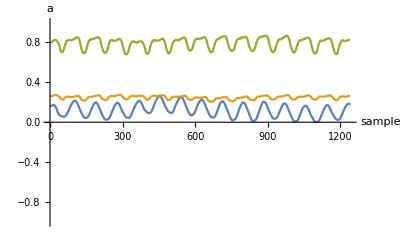

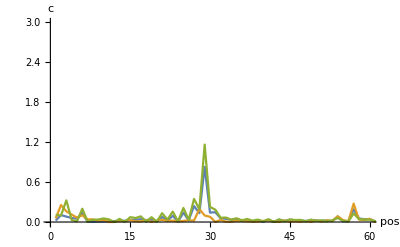

{{29,0.827725},{57,0.276993},{29,1.16448}}

-Graphics-

```mathematica
(*pow = Map[Take[#,Round[rowCount/2]]&,Abs[Fourier[Map[Mean[#]-#&,acceleration]]]];*)
pow = Abs[FourierDST[Map[Mean[#]-#&,acceleration]]];
Length[pow[[1]]]
ListLinePlot[acceleration,{TargetUnits->{"sample","a"},AxesLabel->Automatic,PlotRange->{-1,1}}]
ListLinePlot[pow,{PlotRange->{{0,60},{0,3}},Joined->True,TargetUnits->{"pos","c"},AxesLabel->Automatic}]
maxPowers=Map[{Flatten[Position[#,Max[#]]][[1]],Max[#]}&,pow]
```

(-32.175 | 2.88153
-16.6668 | -3.56369
48.8418 | 0.682158)

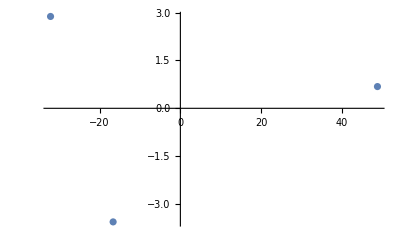

```mathematica
features=FeatureExtract[acceleration];
features//MatrixForm
ListPlot[features,{PlotRange->All}]
```